```mathematica
repAll=Flatten[Table[RepGraph[base],{base,Keys[Bases]}]];
```

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==0//FullSimplify
```

g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35+5 g1x2x3x4x5==2 (g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4)

```mathematica
v=ListofVars[g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35]
```

{g13x24x5,g13x25x4,g14x25x3,g14x2x35,g1x24x35}

```mathematica
Select[Keys[allGraphs5],Length[Intersection[ListofVars[allGraphs5[#,"colofourgenerator"]],{g13x24x5,g13x25x4,g14x25x3,g14x2x35,g1x24x35}]]==5&]
```

{19683,33048,20665,20466,39366,52974,57528,59048,54492,52976,43902,45416,43908,40878,40896,39384,39392,39372,39368,17514,18980,17568,14586,14748,13340,13124,5104,5834,6320,4860,4920,729,1458,1944,2124,1620,1476,243,414,486,666,728,546,488,218,72,9,16,18,26,1,2}

```mathematica
Select[Keys[allGraphs5],Length[Intersection[ListofVars[allGraphs5[#,"colofourgenerator"]],{g13x24x5,g13x25x4,g14x25x3,g14x2x35,g1x24x35}]]==0&]
```

{0,26244,28431,29160,29484,29511,29520,29523,29524,29525,29527,29521,29529,29533,29537,29514,29515,29517,29512,29513,29542,29551,29560,29493,29496,29497,29494,29502,29506,29487,29488,29485,29605,29633,29577,29442,29443,29433,29434,29460,29469,29415,29416,29417,29406,29407,29405,29736,29766,29767,29768,29797,29737,29857,29676,29677,29647,29241,29268,29277,29280,29281,29282,29278,29271,29272,29269,29270,29296,29305,29250,29253,29254,29257,29251,29244,29245,29247,29242,29322,29353,29325,29328,29199,29200,29205,29209,29190,29191,29223,29172,29173,29174,29182,29163,29164,29166,29920,30163,30244,30253,30262,30334,30172,30406,30496,30586,30001,30010,30082,29929,29938,28755,28782,28791,28794,28795,28792,28800,28804,28785,28786,28783,28764,28767,28768,28765,28773,28777,28758,28759,28756,28876,28848,28713,28714,28704,28705,28686,28687,28677,28678,29007,29037,29038,29008,29128,28947,28948,28918,28512,28539,28548,28551,28552,28549,28542,28543,28540,28521,28524,28525,28522,28515,28516,28513,28593,28624,28596,28470,28471,28476,28480,28461,28462,28443,28444,28453,28434,28435,30708,31438,31711,31954,31468,32198,32441,32684,30981,31224,30738,26973,27336,27337,27327,27328,27255,27256,27246,27247,27579,27580,27489,27490,27054,27093,27094,27084,27085,27063,27064,27055,27012,27013,27003,27004,27732,27975,28056,28065,27984,28218,28308,27813,27822,27741,26607,26608,26609,26598,26599,26597,26526,26527,26517,26518,26501,26489,26850,26851,26852,26760,26761,26325,26364,26365,26366,26355,26356,26354,26334,26335,26326,26283,26284,26274,26275,26258,35976,36084,36085,36086,36817,35352,35353,38281,33888,33889,33157,22599,22950,22959,22962,22963,22964,22960,22953,22954,22951,22952,22854,22845,22707,22716,22719,22720,22721,22717,22710,22711,22708,22709,22611,22602,23680,23689,23437,23446,22221,22230,22233,22234,22237,22231,22224,22225,22227,22222,22312,22140,22149,22150,22141,22125,22116,21978,21987,21990,21991,21988,21981,21982,21979,21967,21957,22060,21897,21906,21907,21898,21882,21873,25141,24898,24408,24411,24414,24165,24168,20775,20776,20781,20785,20766,20767,20794,20739,20740,20532,20533,20523,20524,20496,20497,20457,20461,21501,21258,20007,20034,20046,20047,20048,20056,20037,20038,20040,20010,20011,19953,19791,19803,19804,19805,19794,19795,19767,19768,19710,19732,48438,49194,49203,49206,49207,49208,49210,49204,49212,49216,49220,49197,49198,49200,49195,49196,49954,49963,49972,48447,48450,48451,48448,48456,48460,48441,48442,48439,51475,46938,46939,46929,46930,46183,46174,56010,56011,56012,42390,42399,42402,42403,42404,42400,42393,42394,42391,42392,41646,41647,41637,41638,40134,40135,39379,8748,9477,9801,9828,9837,9840,9841,9842,9844,9838,9846,9850,9854,9831,9832,9834,9829,9830,9810,9813,9814,9811,9819,9823,9804,9805,9802,9759,9760,9750,9751,9732,9733,9734,9723,9724,9722,9558,9585,9594,9597,9598,9599,9595,9588,9589,9586,9587,9567,9570,9571,9574,9568,9561,9562,9564,9559,9516,9517,9522,9526,9507,9508,9489,9490,9491,9499,9480,9481,9483,10210,10453,10534,10543,10552,10462,10291,10300,10219,10228,9072,9099,9108,9111,9112,9109,9117,9121,9102,9103,9100,9130,9139,9148,9081,9084,9085,9082,9090,9094,9075,9076,9073,9030,9031,9021,9022,9048,9057,9003,9004,8994,8995,8829,8856,8865,8868,8869,8866,8859,8860,8857,8884,8893,8838,8841,8842,8839,8832,8833,8830,8787,8788,8793,8797,8778,8779,8811,8760,8761,8770,8751,8752,11947,11704,11217,11244,11190,10974,10947,7653,7654,7644,7645,7735,7707,7560,7569,7572,7573,7576,7570,7563,7564,7566,7561,7371,7410,7411,7401,7402,7380,7381,7372,7483,7455,7317,7326,7329,7330,7327,7320,7321,7318,8346,8355,8103,8112,6804,6924,6925,6926,6915,6916,6914,7006,6831,6840,6843,6844,6841,6834,6835,6832,6861,6870,6813,6816,6807,6642,6681,6682,6683,6672,6673,6671,6651,6652,6643,6754,6588,6597,6600,6601,6598,6591,6592,6589,6573,6564,16050,16158,16159,16160,15399,15426,15427,15454,15400,13962,13963,14044,13881,13882,13231,2916,3267,3276,3279,3280,3281,3277,3270,3271,3268,3269,3171,3162,3492,3522,3523,3524,3493,3432,3433,3403,3024,3033,3036,3037,3038,3034,3027,3028,3025,3026,2928,2919,3970,3979,2538,2547,2550,2551,2554,2548,2541,2542,2544,2539,2457,2466,2467,2458,2442,2433,2793,2794,2703,2704,2268,2295,2304,2307,2308,2305,2298,2299,2296,2323,2332,2277,2278,2269,2214,2223,2224,2215,2199,2197,2190,2188,5377,4647,1092,1093,1098,1102,1083,1084,1056,1057,1335,1336,849,850,840,841,813,814,922,756,759,760,757,733,1791,324,351,363,364,365,373,354,355,357,382,327,328,255,606,607,608,108,120,121,122,111,112,90,91,84,85,193,30,31,12,4}

```mathematica
Table[ShowGraph5Least[k],{k,Select[Keys[allGraphs5],Length[Intersection[ListofVars[allGraphs5[#,"colofourgenerator"]],{g13x24x5,g13x25x4,g14x25x3,g14x2x35,g1x24x35}]]==5&]}]
```

{-Graphics-1968321,-Graphics-330485,-Graphics-206653,-Graphics-204665,-Graphics-3936613,-Graphics-529745,-Graphics-575282,-Graphics-590481,-Graphics-544922,-Graphics-529762,-Graphics-439024,-Graphics-454162,-Graphics-439081,-Graphics-408785,-Graphics-408962,-Graphics-393845,-Graphics-393922,-Graphics-393724,-Graphics-393685,-Graphics-175144,-Graphics-189802,-Graphics-175681,-Graphics-145864,-Graphics-147481,-Graphics-133401,-Graphics-131244,-Graphics-51045,-Graphics-58345,-Graphics-63202,-Graphics-48604,-Graphics-49201,-Graphics-72921,-Graphics-145813,-Graphics-19445,-Graphics-21242,-Graphics-16204,-Graphics-14765,-Graphics-24321,-Graphics-4145,-Graphics-48613,-Graphics-6665,-Graphics-7282,-Graphics-5464,-Graphics-4885,-Graphics-2184,-Graphics-724,-Graphics-921,-Graphics-165,-Graphics-1813,-Graphics-265,-Graphics-121,-Graphics-213}

```mathematica
allGraphs5[4920,"colofourgenerator"]/.repAll
```

-Graphics-034--Graphics-291608--Graphics-200348--Graphics-68168--Graphics-22788--Graphics-7608--Graphics-284625--Graphics-263645--Graphics-228543--Graphics-221503--Graphics-207403--Graphics-98285--Graphics-90765--Graphics-75703--Graphics-30365+2 -Graphics-295111+2 -Graphics-294151+-Graphics-292511+2 -Graphics-291911+2 -Graphics-266071+2 -Graphics-222311+2 -Graphics-207671+2 -Graphics-90851+2 -Graphics-75731+2 -Graphics-30371+2 -Graphics-294881+2 -Graphics-294400+2 -Graphics-292801+2 -Graphics-287861+2 -Graphics-287141+2 -Graphics-285521+-Graphics-273340+-Graphics-273100+-Graphics-270941+2 -Graphics-229621+2 -Graphics-229360+2 -Graphics-228820+2 -Graphics-98401+2 -Graphics-98381+2 -Graphics-98321-6 -Graphics-295230-5 -Graphics-295210-6 -Graphics-295150-5 -Graphics-294970-6 -Graphics-294430-5 -Graphics-292810-6 -Graphics-287950-4 -Graphics-273370-6 -Graphics-229630-6 -Graphics-98410+22 -Graphics-295240

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]/.repAll
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820-2 -Graphics-295210-2 -Graphics-294970-2 -Graphics-294430-2 -Graphics-273370-2 -Graphics-229630+5 -Graphics-295240

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,{lambdaKey,starKey}}]]/.repAll
```

-Graphics-294400+-Graphics-292801+-Graphics-287861+-Graphics-285521+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820+-Graphics-98401+-Graphics-98321--Graphics-295230--Graphics-295210--Graphics-295150--Graphics-294970--Graphics-294430--Graphics-292810--Graphics-287950--Graphics-273370--Graphics-229630--Graphics-98410+2 -Graphics-295240

```mathematica
allGraphs5[lambdaKey,"colofourgenerator"]/.repAll
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240

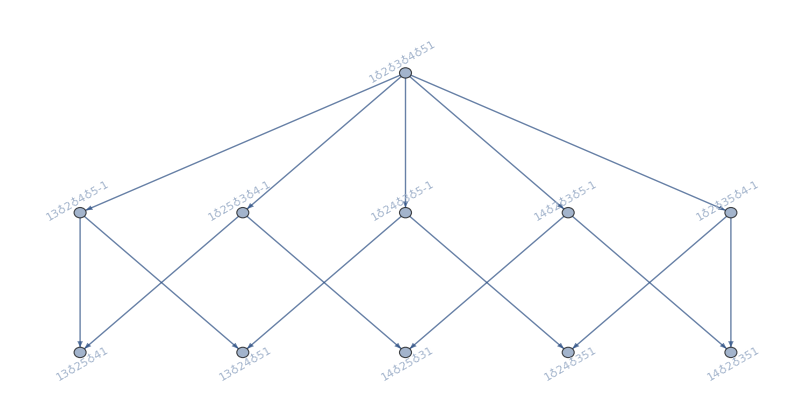

```mathematica
FormulaGraphReverse3[allGraphs5[lambdaKey,"colofourgenerator"]]
```

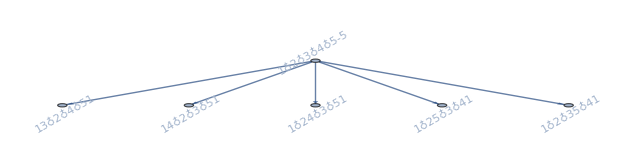

```mathematica
FormulaGraphReverse3[Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]]
```

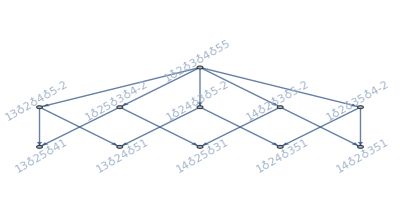

```mathematica
FormulaGraphReverse3[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]]
```

```mathematica
allGraphs5[lambdaKey,"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240

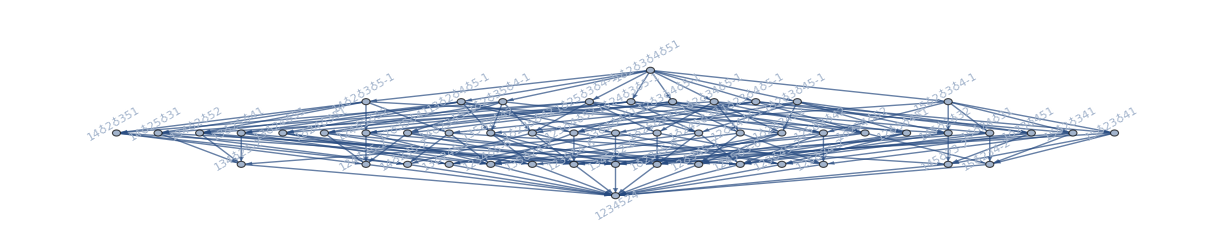

```mathematica
FormulaGraphReverse3[allGraphs5[K5Key,"colofourrealnull"]]
```

```mathematica
allGraphs5[lambdaKey,"colofourrealnull"]/.RepGraph["E"]
```

4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-454162--Graphics-408962--Graphics-393922--Graphics-189802--Graphics-63202--Graphics-21242--Graphics-7282+-Graphics-529745+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-6665+-Graphics-19445+-Graphics-4885+-Graphics-58345+-Graphics-14765+-Graphics-265--Graphics-3936613--Graphics-48613--Graphics-1813--Graphics-145813--Graphics-213+-Graphics-034

```mathematica
f1[x_]:=x^5
```

```mathematica
f2[x_]:=f1[x]-5x^4
```

```mathematica
f3[x_]:=f2[x]+10x^3
```

```mathematica
f4[x_]:=f3[x]-10x^2
```

```mathematica
f5[x_]:=f4[x]+4x
```

```mathematica
Solve[f5[x]-f1[x]==0,x]
```

{{x→0},{x→Root0.755Root[-4+10 #1-10 #1^2+5 #1^3&,1]0.7545378306627368},{x→Root0.623-0.820 ⅈRoot[-4+10 #1-10 #1^2+5 #1^3&,2]0.6227310846686314},{x→Root0.623+0.820 ⅈRoot[-4+10 #1-10 #1^2+5 #1^3&,3]0.6227310846686314}}

```mathematica
f5[x]
```

4 x-10 x^2+10 x^3-5 x^4+x^5

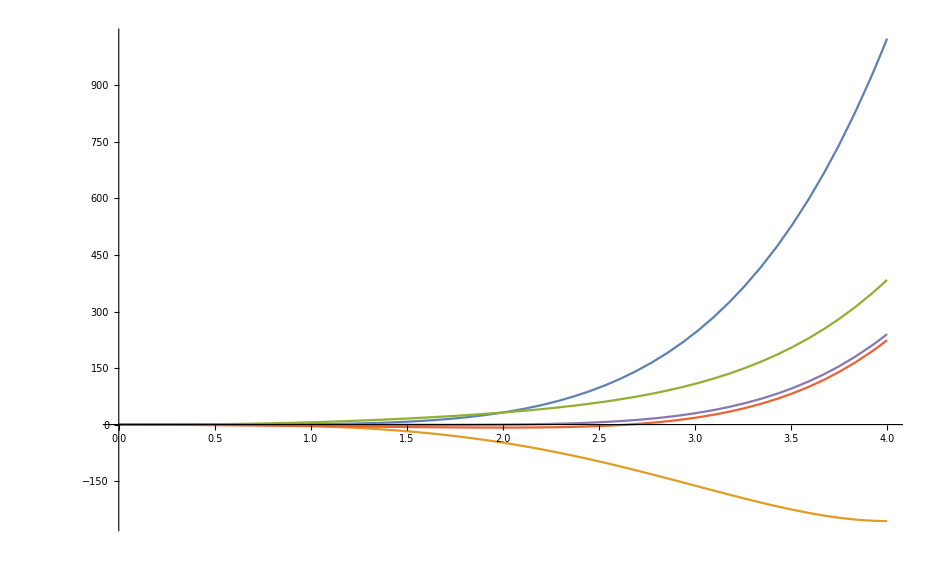

```mathematica
Plot[{f1[x],f2[x],f3[x],f4[x],f5[x]},{x,0,4},PlotRange->All]
```

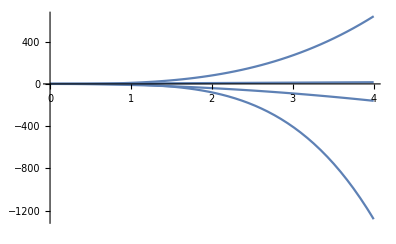

```mathematica
Plot[{f1[x],f2[x],f3[x],f4[x],f5[x]}//Differences,{x,0,4},PlotRange->All]
```

```mathematica
Table[{f1[x],f2[x],f3[x],f4[x],f5[x]}//Differences,{x,0,5}]
```

{{0,0,0,0},{-5,10,-10,4},{-80,80,-40,8},{-405,270,-90,12},{-1280,640,-160,16},{-3125,1250,-250,20}}

```mathematica
Table[StirlingS2[5,x],{x,0,5}]
```

{0,1,15,25,10,1}